# Graph theory, NP hard combinatorial optimization and world geography

Author Name

Abstract

## Section

I can find a graph of all countries in Eurasia

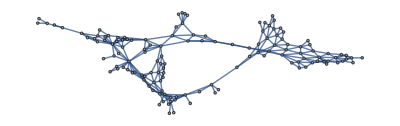

```mathematica
ℰ=NestGraph[CountryData[#,"BorderingCountries"]&,Entity["Country","France"],12];
ℰ=UndirectedGraph[ℰ,ImageSize->Full,VertexLabels->(Normal@AssociationMap[Placed[Labeled[#["FlagImage"],#["Name"]],Tooltip]&,VertexList[ℰ]])]
```

Analyze the structure of the graph. What countries are farthest away and how far are they?

```mathematica
mostDistantCountries=GraphPeriphery[ℰ]
```

GraphPeriphery[ℰ]

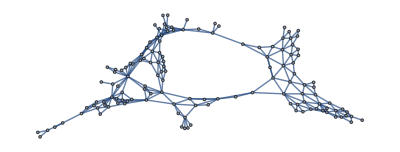

```mathematica
𝒥=NestGraph[CountryData[#,"BorderingCountries"]&,Entity["Country","Jordan"],9];
𝒥=UndirectedGraph[𝒥,ImageSize->Full,VertexLabels->(Normal@AssociationMap[Placed[Labeled[#["FlagImage"],#["Name"]],Tooltip]&,VertexList[𝒥]])]
```

```mathematica
ℰ
```

-Graphics-

```mathematica
CommunityGraphPlot[ℰ]
```

-Graphics-

```mathematica
AssociationMap[GraphPeriphery[𝒥,Method->#]&,{"Dijkstra","FloydWarshall","Johnson","PseudoDiameter"}]
```

<|Dijkstra→{East Timor,Papua New Guinea,Lesotho},FloydWarshall→{East Timor,Papua New Guinea,Lesotho},Johnson→{East Timor,Papua New Guinea,Lesotho},PseudoDiameter→{}|>

```mathematica
GraphCenter[ℰ]
```

{Syria,Jordan}

```mathematica
GraphCenter[𝒥]
```

{}

```mathematica
Map[GraphPeriphery[#]&,{ℰ,𝒥}]
```

{{East Timor,Papua New Guinea,Lesotho},{}}

```mathematica
Map[GraphRadius[#]&,{ℰ,𝒥}]
```

{9,∞}

```mathematica
Map[GraphDiameter[#]&,{ℰ,𝒥}]
```

{18,∞}

```mathematica
Map[GraphCenter[#]&,{ℰ,𝒥}]
```

{{Syria,Jordan},{}}

Make a manipulate for FindShortestPath.

```mathematica
Manipulate[Plot[Sin[a x]+base,{x,0,10},Filling->axisfilling,PlotStyle->{Directive[color,AbsoluteThickness[thickness]]},Axes->axes],
{a,1,10},{axes,{True,False}},{{color,Orange},{Red,Orange,Yellow,Green,Blue,Purple}},{thickness,Range[1,10],ControlType->RadioButtonBar},{axisfilling,{None,Axis,Bottom,Top}},{base,-1,1}]
```

```mathematica
Manipulate[x,{x,0,1,ControlType->IntervalSlider}]
```

```mathematica
Manipulate[x,{x,0,1,ControlType->Animator,AnimationRunning->False}]
```